```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/fluc_T/fluctuations_T/highorder_2p1/input_h/finitemub_v4/fluc_Tc230a0p5_h14/mub175/data

### Model

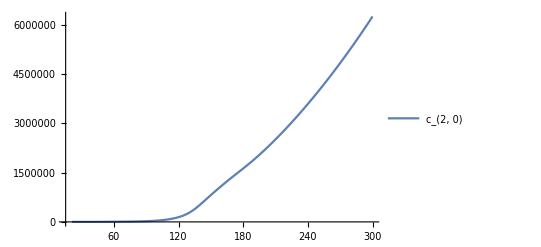

```mathematica
chi0=Flatten[Import["./chi0.dat"]];
chi1=Flatten[Import["./chi1.dat"]];
chi2=Flatten[Import["./chi2.dat"]];
chi3=Flatten[Import["./chi3.dat"]];
chi4=Flatten[Import["./chi4.dat"]];
chi5=Flatten[Import["./chi5.dat"]];
chi6=Flatten[Import["./chi6.dat"]];
chi7=Flatten[Import["./chi7.dat"]];
chi8=Flatten[Import["./chi8.dat"]];
T=Flatten[Table[21+(i-1),{i,1,280}]];
cs2=Transpose[{T/184,chi1/(T*chi2)}];
ListLinePlot[Transpose[{T,chi2}],PlotRange->All,PlotLegends->{"c_(2, 0)"}]
```

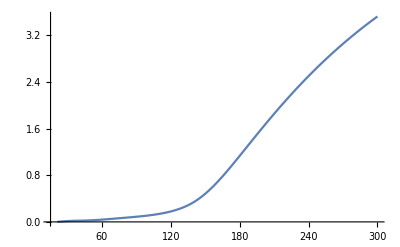

```mathematica
ListLinePlot[Transpose[{T,(chi0-chi0[[1]])/T^4}],PlotRange->All]
```

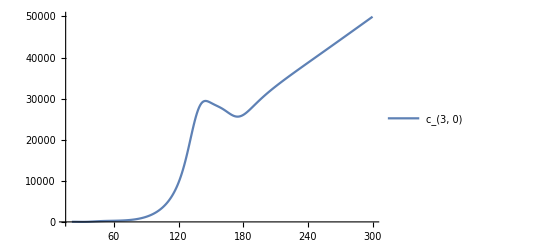

```mathematica
ListLinePlot[Transpose[{T,chi3}],PlotRange->{All,{-0000,50000}},PlotLegends->{"c_(3, 0)"}]
```

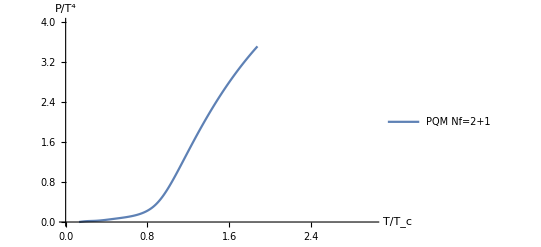

```mathematica
PlotP=Show[ListLinePlot[{Transpose[{T/160,(chi0-chi0[[1]])/T^4}],Hotpdown,Hotpup},Filling->{2->{3}},FillingStyle->LightRed,PlotStyle->{Automatic,None,None},PlotLegends->{"PQM Nf=2+1"},PlotRange->{{0.,3},{0,4}}],ListLinePlot[{WBdown,WBup},Filling->{1->{2}},PlotStyle->{None}],AxesLabel->{"T/T_c","P/T^4"}]
```

## Temperature Fluctuations

```mathematica
c1=chi1;
c2=T^2(1/chi2)^1;
c3=-T^5(1/chi2)^3(chi3);
c4=T^8(3(1/chi2)^5(chi3)^2-(1/chi2)^4 chi4);
c5=T^11(-15(1/chi2)^7(chi3)^3-(1/chi2)^5 chi5+10(1/chi2)^6 chi3 chi4);
c6=T^14(105(1/chi2)^9 chi3^4-105(1/chi2)^8 chi3^2 chi4+10(1/chi2)^7 chi4^2+15(1/chi2)^7 chi3 chi5-(1/chi2)^6 chi6);
Export["./c2.dat",c2];
Export["./c3.dat",c3];
Export["./c4.dat",c4];
Export["./c5.dat",c5];
Export["./c6.dat",c6];
```

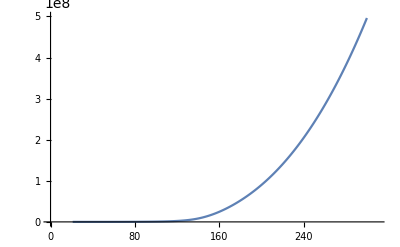

```mathematica
ListLinePlot[Transpose[{T,chi1}],PlotRange->{{0,310},{0.01,5*10^8}},ScalingFunctions->Automatic]
```

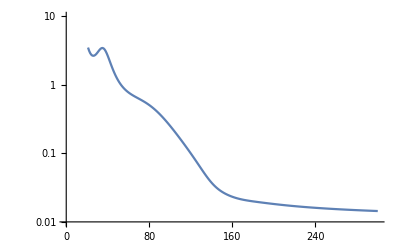

```mathematica
ListLinePlot[Transpose[{T,c2}],PlotRange->{{0,300},{0.01,10}},ScalingFunctions->"Log"]
```

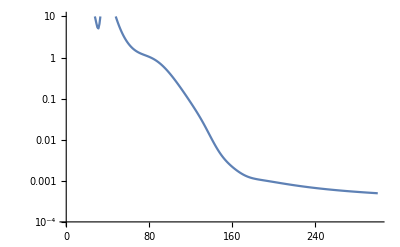

```mathematica
ListLinePlot[Transpose[{T,-c3}],PlotRange->{{0,300},{10,0.0001}},ScalingFunctions->"Log"]
```

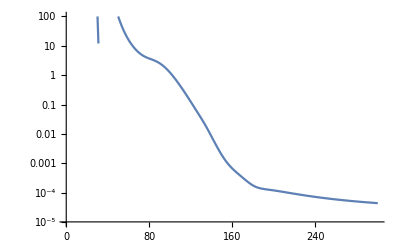

```mathematica
ListLinePlot[Transpose[{T,c4}],PlotRange->{{0,300},{0.00001,100}},ScalingFunctions->"Log"]
```